```mathematica
SetDirectory[NotebookDirectory[]];
bandStats=Import["../data/out/band_stats.tsv","HeaderLines"->1];
```

Mean time (ms) to compute matching between two curves without bands:

```mathematica
N@Mean[bandStats[[All,4]]]
```

66.49

Mean time (ms) to compute matching between two curves with bands:

```mathematica
N@Mean[bandStats[[All,2]]]
```

4.51

```mathematica
sortedStats=SortBy[bandStats,#[[3]]&];
```

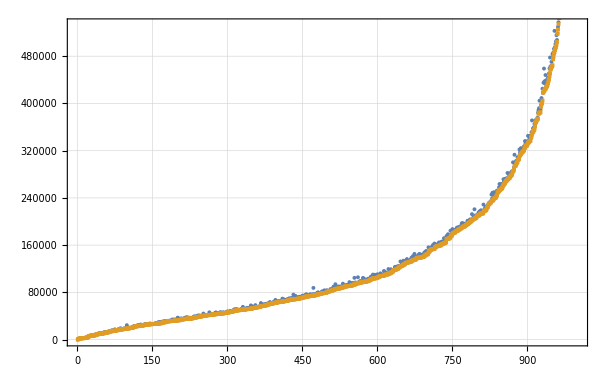

```mathematica
ListPlot[
{sortedStats[[All,1]],sortedStats[[All,3]]},
PlotTheme->"Detailed",PlotMarkers->{Automatic,Tiny},
Epilog->Inset[Framed[ResourceFunction["RecordsSummary"][absCostError][[1,1,2]]],ImageScaled[{0,1}],ImageScaled[{-0.55,1.1}]]
]
```

```mathematica
nonZeroStats=Select[bandStats,#[[3]]≠0&];
absCostError=#[[1]]-#[[3]]&/@nonZeroStats;
relCostError=(#[[1]]-#[[3]])/#[[3]]&/@nonZeroStats;
```

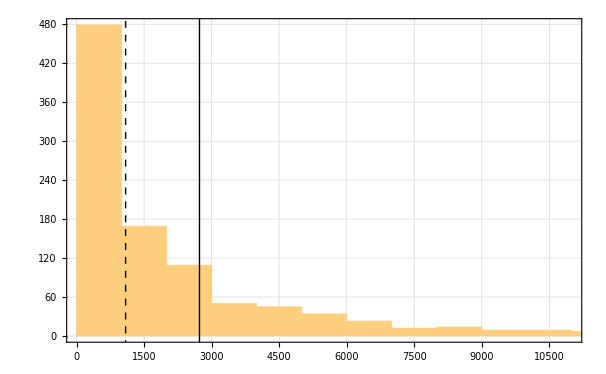

```mathematica
Show[
Histogram[absCostError,PlotTheme-> "Detailed"],
Epilog->{
InfiniteLine[{Mean[absCostError],0},{0,1}],
{Dashed,InfiniteLine[{Median[absCostError],0},{0,1}]},
Inset[Framed[ResourceFunction["RecordsSummary"][absCostError][[1,1,2]]],ImageScaled[{1,1}],ImageScaled[{1.1,1.1}]]
}
]
```

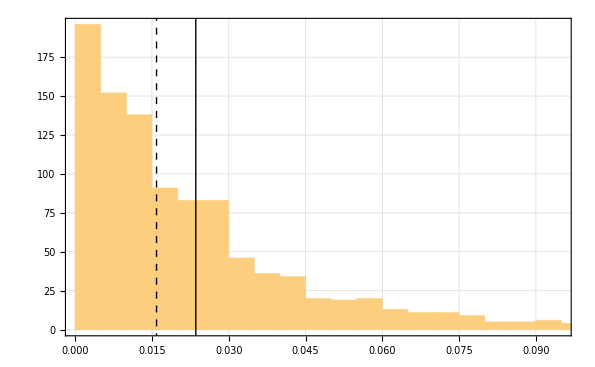

```mathematica
Show[
Histogram[relCostError,PlotTheme-> "Detailed"],
Epilog->{
InfiniteLine[{Mean[relCostError],0},{0,1}],
{Dashed,InfiniteLine[{Median[relCostError],0},{0,1}]},
Inset[Framed[ResourceFunction["RecordsSummary"][relCostError][[1,1,2]]],ImageScaled[{1,1}],ImageScaled[{1.1,1.1}]]
}
]
```